## Cross-correlation Plotter

Date: 06-12-2021

```mathematica
Needs["ErrorBarPlots`"]
SetDirectory[NotebookDirectory[]];
dirstring = "\\"; (*may be adjusted if your operating system uses another convention for directory paths*)
```

#### Used Functions (New Equate Lengths and σ)

```mathematica
WA[CCsdatalist_]:= Module[{returnlist,Nw},
Nw = Sum[1/CCsdatalist⟦iexp,All,3⟧^2,{iexp,1,Length[CCsdatalist]}];
returnlist=Sum[CCsdatalist⟦iexp,All,2⟧/CCsdatalist⟦iexp,All,3⟧^2,{iexp,1,Length[CCsdatalist]}]/Nw
];
σA[CCsdatalist_]:=Module[{nexp,returnlist,Nw,sμ2,si2, μlist,ni,σ2},
nexp = Length[CCsdatalist];
ni = 4;
si2 = CCsdatalist⟦All,All,3⟧ᵀ;
sμ2= Table[Variance[CCsdatalist⟦All,All,2⟧ᵀ⟦i⟧],{i,Length[CCsdatalist⟦All,All,2⟧ᵀ]}];

σ2=(sμ2 Sum[ni^2,{i,1,nexp}]+Sum[ni si2⟦All,i⟧,{i,nexp}])/Sum[ni,{i,1,nexp}]^2;
 Return[√σ2]

];



(*Used to prepare lists that can be ErrorListPlotted. Assumes experiments have equal time lengths *)

PrepPlot[CCsdatalist_]:=Module[{Wsum, σ,returnlist,time,iexp,Nw},{
returnlist = {};
Wsum = WA[CCsdatalist];
σ=σA[CCsdatalist];

time =Sum[CCsdatalist⟦iexp,All,1⟧,{iexp,1,Length[CCsdatalist]}]/Length[CCsdatalist];

AppendTo[returnlist, Table[{{time⟦itime⟧,Wsum⟦itime⟧},ErrorBar[0]},{itime,1,Length[time]}]];
AppendTo[returnlist,  Table[{{time⟦itime⟧,Wsum⟦itime⟧},ErrorBar[σ⟦itime⟧]},{itime,1,Length[time],5}]];

For[iexp = 1, iexp≤ Length[CCsdatalist],iexp++,{
AppendTo[returnlist,Table[{{time⟦itime⟧,CCsdatalist⟦iexp,itime,2⟧},ErrorBar[0]},{itime,1,Length[time]}]];
AppendTo[returnlist, Table[{{time⟦itime⟧,CCsdatalist⟦iexp,itime,2⟧},ErrorBar[CCsdatalist⟦iexp,itime,3⟧]},{itime,iexp,Length[time],5}]];
}];

Return[returnlist]}]⟦1⟧
```

```mathematica
intraval[tx_,list_,i_]:= 
Module[{y1,y2,t1,t2,t0,s1,s2,sx, y,s},
{t1,y1,s1} = list⟦i-1⟧;
{t2,y2,s2} = list⟦i⟧;
 y=y1 + (y2-y1)/(t2-t1)(tx-t1);
s = s1 + (s2-s1)/(t2-t1)(tx-t1);
Return[{tx,y,s}]
];

intralist[list_,times_,t0_,tend_]:=Module[{eqtimelist,i,j,tx},
tx = t0;  eqtimelist = {}; i= 1;j = 1;
While[j≤ Length[times],{tx = times⟦j⟧,
If[tx > list⟦i,1⟧,i++,{AppendTo[eqtimelist,intraval[tx,list,i]],j =j+1}]}];
Return[eqtimelist]];

EquateLengths[CCsdatalist_]:=
 Module[{pickitime, time,dt,t0, tend,equallist,iloop},
pickitime=Position[-CCsdatalist⟦All,1,1⟧,Min[-CCsdatalist⟦All,1,1⟧]]⟦1,1⟧;
time = CCsdatalist⟦pickitime,All,1⟧;
t0 = time⟦1⟧; tend = time⟦-1⟧;
equallist = {CCsdatalist⟦pickitime⟧};
iloop = 1;
While[iloop≤ Length[CCsdatalist⟦All,1,1⟧], If[iloop ≠ pickitime, {AppendTo[equallist,intralist[CCsdatalist⟦iloop⟧,time,t0,tend]],iloop = iloop+1},iloop=iloop+1]];
Return[equallist]
]
```

#### Used Stylization

```mathematica
opac =.2;
styleWAϕ = {Darker[Black]};
styleWAπ = {Darker[Black],Dashed};
styleϕ = {Darker[Blue],Opacity[opac]};
styleπ = {Darker[Blue],Dashed,Opacity[opac]};
styleπE = {Darker[Blue],Opacity[opac]};
joinedlist ={True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False};
```

Wild Type

#### WT ϕ-λ

```mathematica
SetDirectory[NotebookDirectory[]<>dirstring<>"WT_lac"]; 

name = "WT_" ;(*Set the basal name of these experiments*)
nexp = 6; (*Set the number of experiments done for this strain*)

SetOptions[ListPlot,{PlotRange-> {All,{-.5,.5}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9,
Joined-> joinedlist,PlotStyle-> {styleWAϕ,styleWAϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ}}];

ϕYμWT = {};
For[iexp = 1,iexp≤ nexp,iexp++,AppendTo[ϕYμWT,Import[name<>ToString[iexp]<>"_phiY_mu.dat","CSV"]];] ;Clear[iexp];
ϕYμWT = EquateLengths[ϕYμWT];

ϕHμWT = {};
For[iexp = 1,iexp≤ nexp,iexp++,AppendTo[ϕHμWT,Import[name<>ToString[iexp]<>"_phiH_mu.dat","CSV"]];];Clear[iexp];
ϕHμWT = EquateLengths[ϕHμWT];

plotϕYμWT =  ErrorListPlot[PrepPlot[ϕYμWT]];
plotϕHμWT = ErrorListPlot[PrepPlot[ϕHμWT]];
```

#### WT π-λ

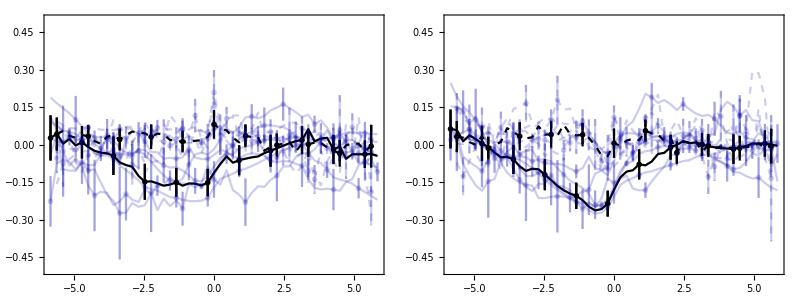

```mathematica
SetDirectory[NotebookDirectory[]<>dirstring<>"WT_lac"]; 

name = "WT_" ;(*Set the basal name of these experiments*)
nexp = 6; (*Set the number of experiments done for this strain*)
SetOptions[ListPlot,{PlotRange-> {All,{-.5,.5}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9,
Joined-> joinedlist,PlotStyle-> {styleWAπ ,styleWAϕ,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ}}];

πYμWT = {};
For[iexp = 1,iexp≤ nexp,iexp++,AppendTo[πYμWT,Import[name<>ToString[iexp]<>"_piY_mu.dat","CSV"]];] ;Clear[iexp];
πYμWT = EquateLengths[πYμWT];

πHμWT = {};
For[iexp = 1,iexp≤ nexp,iexp++,AppendTo[πHμWT,Import[name<>ToString[iexp]<>"_piH_mu.dat","CSV"]];];Clear[iexp];
πHμWT = EquateLengths[πHμWT];



plotπYμWT =  ErrorListPlot[PrepPlot[πYμWT]];
plotπHμWT = ErrorListPlot[PrepPlot[πHμWT]];
plotWT ={{Show[plotϕYμWT,plotπYμWT],Show[plotϕHμWT,plotπHμWT]}}//TableForm
```

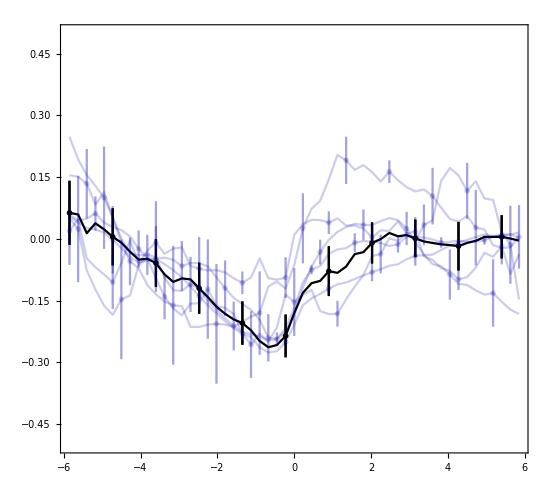
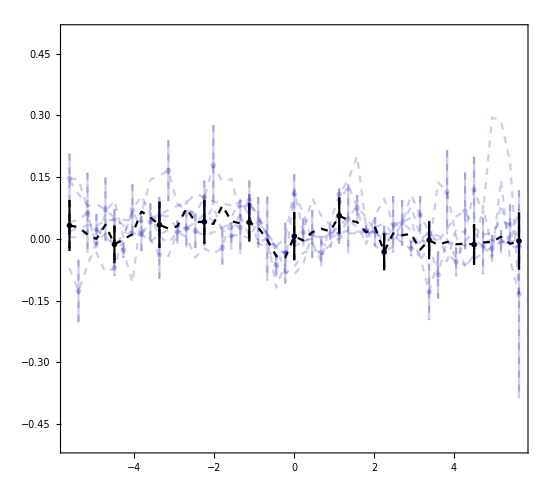

```mathematica
{Show[plotϕHμWT],Show[plotπHμWT]}
```

#### WT πy-πh

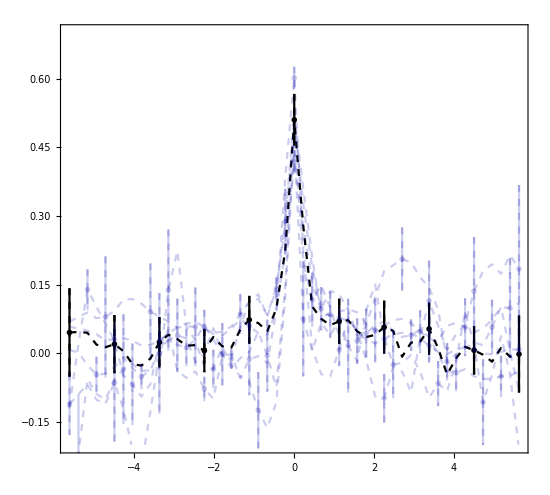

```mathematica
SetDirectory[NotebookDirectory[]<>dirstring<>"WT_lac"]; 

name = "WT_" ;(*Set the basal name of these experiments*)
nexp = 6; (*Set the number of experiments done for this strain*)
SetOptions[ListPlot,{PlotRange-> {All,{-.2,.7}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9,
Joined-> joinedlist,PlotStyle-> {styleWAπ ,styleWAϕ,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ}}];

πHπYWT = {};
For[iexp = 1,iexp≤ nexp,iexp++,AppendTo[πHπYWT,Import[name<>ToString[iexp]<>"_piH_piY.dat","CSV"]];] ;Clear[iexp];
πHπYWT = EquateLengths[πHπYWT];


plotπHπYWT =  ErrorListPlot[PrepPlot[πHπYWT]]
```

Mutant

### Low

#### Low ϕ-λ

```mathematica
SetDirectory[NotebookDirectory[]<>dirstring<>"MUT_low"]; name1 = "MUT_low_1_"; name2 = "MUT_low_2_";

SetOptions[ListPlot,{Joined-> joinedlist,PlotRange-> {All,{-0.5,0.5}},PlotStyle-> {{Black},{Black},styleϕ,styleϕ,styleϕ,styleϕ},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9}];

ϕYμLOW ={Import[name1<>"phiY_mu.dat", "CSV"], Import[name2<>"phiY_mu.dat","CSV"]};
ϕHμLOW ={Import[name1<>"phiH_mu.dat", "CSV"], Import[name2<>"phiH_mu.dat","CSV"]};

ϕYμLOW = EquateLengths[ϕYμLOW];
ϕHμLOW = EquateLengths[ϕHμLOW];

plotϕYμLOW=ErrorListPlot[PrepPlot[ϕYμLOW]];
plotϕHμLOW=ErrorListPlot[PrepPlot[ϕHμLOW]];
```

#### Low π-λ

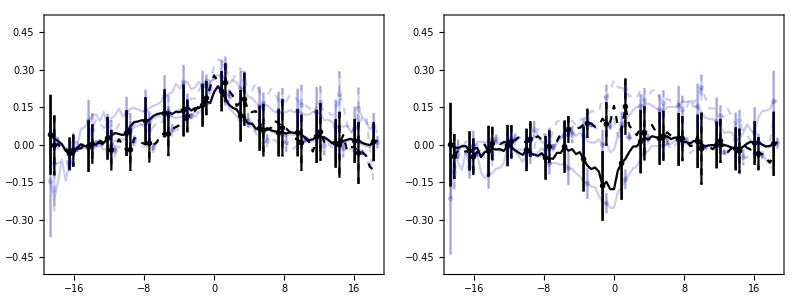

```mathematica
SetDirectory[NotebookDirectory[]<>dirstring<>"MUT_low"]; name1 = "MUT_low_1_"; name2 = "MUT_low_2_";
SetOptions[ListPlot,{Joined-> joinedlist,PlotRange-> {All,{-0.5,0.5}},PlotStyle-> {{Black,Dashed},{Black},styleπ,styleπE,styleπ,styleπE},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9}];

πYμLOW ={Import[name1<>"piY_mu.dat", "CSV"],Import[name2<>"piY_mu.dat","CSV"]};
πHμLOW ={Import[name1<>"piH_mu.dat", "CSV"],Import[name2<>"piH_mu.dat","CSV"]};

πYμLOW = EquateLengths[πYμLOW];
πHμLOW= EquateLengths[πHμLOW];

plotπYμLOW = ErrorListPlot[PrepPlot[πYμLOW]];
plotπHμLOW = ErrorListPlot[PrepPlot[πHμLOW]];

plotMUTLOW = {{Show[{plotϕYμLOW,plotπYμLOW}],Show[plotϕHμLOW,plotπHμLOW]}}//TableForm
```

#### Low πy-πh

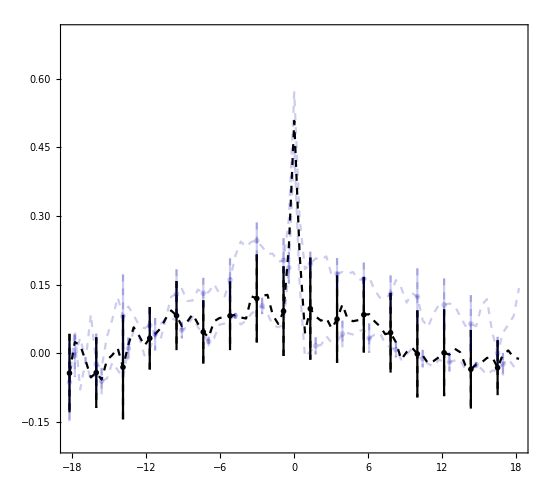

```mathematica
SetOptions[ListPlot,{PlotRange-> {All,{-.2,.7}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9,
Joined-> joinedlist,PlotStyle-> {styleWAπ ,styleWAϕ,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ}}];

πHπYMUTLOW ={Import[name1<>"piH_piY.dat", "CSV"],Import[name2<>"piH_piY.dat","CSV"]};
πHπYMUTLOW = EquateLengths[πHπYMUTLOW];

plotπHπYMUTLOW =  ErrorListPlot[PrepPlot[πHπYMUTLOW]]
```

### Optimal

```mathematica
SetDirectory[NotebookDirectory[]<>dirstring<>"MUT_opt"]; 

name = "MUT_opt_" ;(*Set the basal name of these experiments*)
nexp = 4; (*Set the number of experiments done for this strain*)
```

#### Opt ϕ-λ

```mathematica
SetOptions[ListPlot,{PlotRange-> {All,{-.5,.5}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9,
Joined-> joinedlist,PlotStyle-> {styleWAϕ,styleWAϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ}}];

ϕYμOPT = {};
For[iexp = 1,iexp≤ nexp,iexp++,AppendTo[ϕYμOPT,Import[name<>ToString[iexp]<>"_phiY_mu.dat","CSV"]];] ;Clear[iexp];
ϕYμOPT = EquateLengths[ϕYμOPT];

ϕHμOPT = {};
For[iexp = 1,iexp≤ nexp,iexp++,AppendTo[ϕHμOPT,Import[name<>ToString[iexp]<>"_phiH_mu.dat","CSV"]];];Clear[iexp];
ϕHμOPT = EquateLengths[ϕHμOPT];

plotϕYμOPT =  ErrorListPlot[PrepPlot[ϕYμOPT]];
plotϕHμOPT = ErrorListPlot[PrepPlot[ϕHμOPT]];
```

#### Opt π-λ

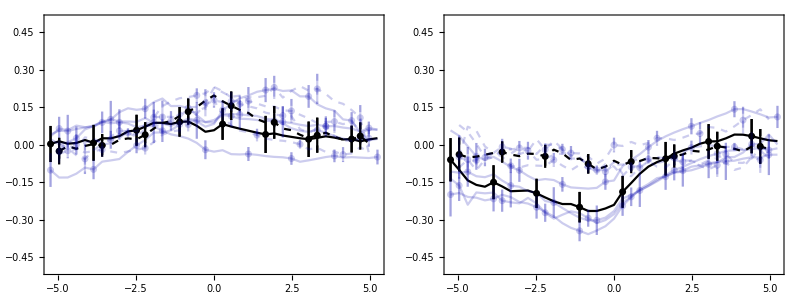

```mathematica
SetOptions[ListPlot,{PlotRange-> {All,{-.5,.5}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9,
Joined-> joinedlist,
PlotStyle-> {styleWAπ,styleWAϕ,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ}}];

πYμOPT = {};
For[iexp = 1,iexp≤ nexp,iexp++,AppendTo[πYμOPT,Import[name<>ToString[iexp]<>"_piY_mu.dat","CSV"]];] ;Clear[iexp];
πYμOPT = EquateLengths[πYμOPT];

πHμOPT = {};
For[iexp = 1,iexp≤ nexp,iexp++,AppendTo[πHμOPT,Import[name<>ToString[iexp]<>"_piH_mu.dat","CSV"]];];Clear[iexp];
πHμOPT = EquateLengths[πHμOPT];



plotπYμOPT =  ErrorListPlot[PrepPlot[πYμOPT]];
plotπHμOPT = ErrorListPlot[PrepPlot[πHμOPT]];
plotMUTOPT ={{Show[plotϕYμOPT,plotπYμOPT],Show[plotϕHμOPT,plotπHμOPT]}}//TableForm
```

#### Opt πy-πh

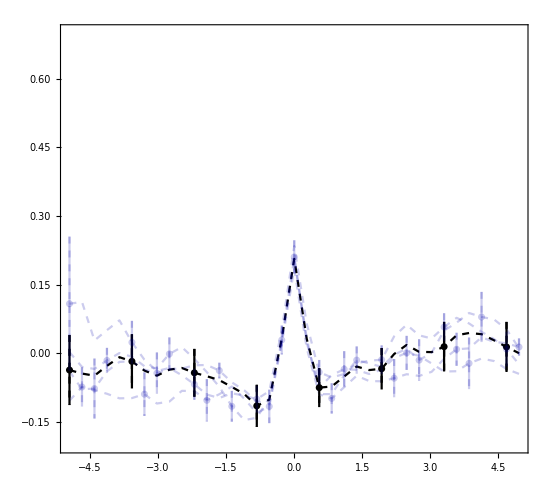

```mathematica
SetOptions[ListPlot,{PlotRange-> {All,{-.2,.7}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9,
Joined-> joinedlist,PlotStyle-> {styleWAπ ,styleWAϕ,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ}}];

πHπYMUT = {};
For[iexp = 1,iexp≤ nexp,iexp++,AppendTo[πHπYMUT,Import[name<>ToString[iexp]<>"_piH_piY.dat","CSV"]];] ;Clear[iexp];
πHπYMUT = EquateLengths[πHπYMUT];

plotπHπYMUT =  ErrorListPlot[PrepPlot[πHπYMUT]]
```

### High

#### High ϕ-λ

```mathematica
SetDirectory[NotebookDirectory[]<>dirstring<>"MUT_high"]; name1 = "MUT_high_1_";  name2 = "MUT_high_2_";
SetOptions[ListPlot,{PlotRange-> {All,{-1,1}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9,
Joined-> joinedlist,PlotStyle-> {{Black},{Black},styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ,styleϕ}}];


ϕYμHIGH ={Import[name1<>"phiY_mu.dat", "CSV"],Import[name2<>"phiY_mu.dat","CSV"]};
ϕHμHIGH ={Import[name1<>"phiH_mu.dat", "CSV"],Import[name2<>"phiH_mu.dat","CSV"]};

ϕYμHIGH = EquateLengths[ϕYμHIGH];
ϕHμHIGH = EquateLengths[ϕHμHIGH];

plotϕYμHIGH= ErrorListPlot[PrepPlot[ϕYμHIGH]];
plotϕHμHIGH= ErrorListPlot[PrepPlot[ϕHμHIGH]];
```

#### High π-λ

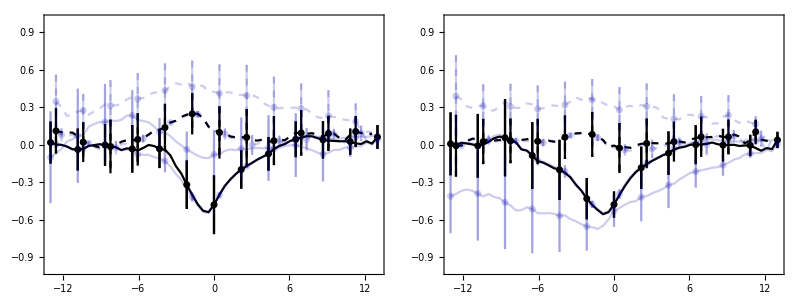

```mathematica
SetDirectory[NotebookDirectory[]<>dirstring<>"MUT_high"]; name1 = "MUT_high_1_";  name2 = "MUT_high_2_";
SetOptions[ListPlot,{PlotRange-> {All,{-1,1}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9,
Joined-> joinedlist,
PlotStyle-> {{Black,Dashed},{Black},styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ}}];


πYμHIGH ={Import[name1<>"piY_mu.dat", "CSV"], Import[name2<>"piY_mu.dat","CSV"]};
πHμHIGH ={Import[name1<>"piH_mu.dat", "CSV"], Import[name2<>"piH_mu.dat","CSV"]};

πYμHIGH = EquateLengths[πYμHIGH];
πHμHIGH=  EquateLengths[πHμHIGH];


plotπYμHIGH=ErrorListPlot[PrepPlot[πYμHIGH]];
plotπHμHIGH=ErrorListPlot[PrepPlot[πHμHIGH]];
plotMUTHIGH={{Show[plotϕYμHIGH,plotπYμHIGH],Show[plotϕHμHIGH,plotπHμHIGH]}}//TableForm
```

#### High πy-πh

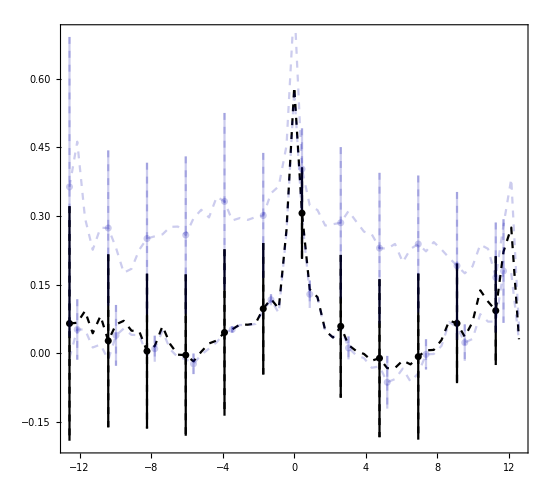

```mathematica
SetOptions[ListPlot,{PlotRange-> {All,{-.2,.7}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9,
Joined-> joinedlist,PlotStyle-> {styleWAπ ,styleWAϕ,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ,styleπE,styleπ}}];

πHπYMUTHIGH ={Import[name1<>"piH_piY.dat", "CSV"],Import[name2<>"piH_piY.dat","CSV"]};
πHπYMUTHIGH = EquateLengths[πHπYMUTHIGH];

plotπHπYMUTHIGH =  ErrorListPlot[PrepPlot[πHπYMUTHIGH]]
```